```mathematica
Code -  

Closing wells; fossil development and abandonment in the energy transition;
```

```mathematica
(* 

This Mathematica code simulates the model in van den Bijgaart & Rodriguez (2023) Closing wells: fossil development and abandonment in the energy transition, Resource and Energy Economics. See this article, in particular Appendix C, for furher details. 

Contact:
Inge van den Bijgaart: i.m.vandenbijgaart@uu.nl
Mauricio Rodriguez Acosta: <mauricio.rodriguezacosta@tno.nl

 *)
```

```mathematica
Initialization;
```

```mathematica
Clear["Global`*"]

(* Adjust code to set directory *)
SetDirectory["C:\\Users\\Bijga001\\Dropbox\\PC\\Documents\\Mathematica_output\\tmp"];
```

```mathematica
Parameterization;

Energy demand eq (18);
epsi=0.6;
chi=71976;

Development cost  eq (19);
omega=9.994*10^-4;
rho=5.191*10^-3;
theta = 2.8819;
psi=0.0512;

Renewable investment cost  eq (20);
xi=609.4;

CCS parameters  eq (C.1);
zi=40;
ziH=330;
(* enter here the number of years after which CCS becomes available. set equal to T for the non-CCS scenarios *)
ccslag=10;

Other fossil extraction parameters ;
cF=10;
kappa=0.073;

Other renewable energy  parameters ;
cR =0;
delta=0.045;

Other  parameters ;
r=0.04;

Initial values state variables ;
startS=759;
startK=19.2;
startU=7903;

Carbon budgets;
(* order budget levels from high to low *)
budgetlevels={2872,2293,1723,1086,869,652};
budgetlength=Length[budgetlevels];

Tax postponement;
(* number of years of tax postponement. Set equal to 0 if not tax delay *)
taxpost=0;
```

```mathematica
Simulation settings;
(* This lists some settings for the simulation. h is the step size per iteration, with h=0.25 denoting quarterly and h=1 annual steps. prec is the targeted precision for the price series. hori is the years for convergence. Conv dictates how quickly each the price and development series are updates with each proposed solution. Higher values imply more series persistence but also greater stability of the solution algorithm. *)

h=1; (* set to .25 before *)
prec=1*10^-4; (*set to 4 before*)
hori=500;
(*Use T=Round[500/h] instead of T=500/h*)
(*T=500/h;*)
T=Round[hori/h];
conv=40;
```

```mathematica
Vectors to store results;
allp={};
allK={};
allEF={};
allE={};
allX={};
allS={};
allcumF={};
allcumX={};
allcons={};
allcx0={};
allinv={};
allU={};
alltax={};
allCCS={};
```

```mathematica
Solution algorithm;
(* See section C.2 for a characterization of the solution algorithm. A given initial tax level and increase as described by Lemma 1 implies a particular level of cumulative emissions, with higher initial taxes associated with lower cumulative emissions. The algorithm for the budget exploits this property by searching for the tax level that ensures cumulative emissions are equal to the defined budget. *)
```

1  gap= 1072.29

101  gap= 0.86172

201  gap= 0.118595

301  gap= 0.0105252

401  gap= 0.00128319

501  gap= 0.000201294

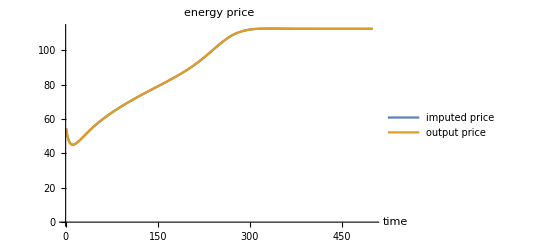

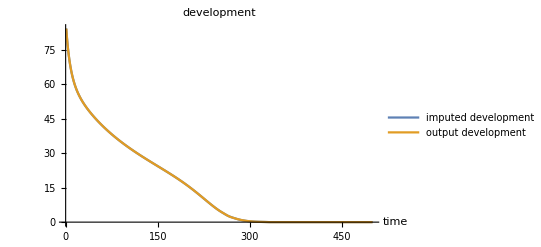

```mathematica
Laissez-faire;
(* simulation with constant taxes. Set tax=0 for laissez-faire *)
tax={0};
taxlength=Length[tax];


For[i=1,i≤ taxlength,
tau=tax[[i]]*0.35;
(* generate the tax series: zero for laissez-faire *)
tau0=Table[tau,T-taxpost/h];
tau0=PadLeft[tau0,T];

Determining steady state values;
(* This specifies steady state levels of renewable capital, prices and shadow values.  *) 
Kss=x/.FindRoot[cR+(r+delta)*xi*(delta*x)==chi*(x^-(1/epsi)),{x,0.0001}];
pEss= chi*(Kss)^-(1/epsi);
muSss=Max[0,(pEss-cF-tau)*kappa/(r+kappa)];
muUss=0;
muKss=xi*(delta*Kss);

(* Determine the maximum value of stock that is left unexplored in steady state. *)
Utilde=x/.FindRoot[muSss==(1+psi)*(theta/(1-Exp[-omega*x])+rho*(startU-x)),{x,0.0001}];


Initialization; 
(* propose a first price series: smooth function between initial price at full extraction & steady state price *)
startP=chi*(kappa*startS+startK)^-(1/epsi);
p0=Table[(1-i/T)*startP+(i/T)*pEss,{i,T}];

(* propose a first development series: exponentially declining or zero *)
If[startU>Utilde,
beta=(h*50)/(startU-Utilde);
x0=(1/h)*Table[beta*Exp[-beta*i]*(startU-Utilde)/(1-Exp[-beta*T]),{i,T}];
,
x0=Table[0,T];
];

(* propose final level of undeveloped stock *)
u0=Utilde;

(* clear previous iteration *)
Clear[fullMuKR, fullMuSR, fullMuK, fullMuS, fullK, fullS, fullp,fulleF, fullinv,fullxpl, fullcons];
z=1;
Z=1;

(* ensure that initial deviation does not lead the series to abort *)
dev=1;

Solution algorithm;
While[dev>prec, 
(* initialization for backward loop; shadow values *)
t=1;
muKR=muKss;
fullMuKR={muKR};
muSR=muSss;
fullMuSR={muSR};
muUR= muUss; 
fullMuUR={muUR};
uR=u0;

(* backward loop to determine co-states: mu's; p0[[-m]] mth to the last element of p0*)
While[t<T,
pE=p0[[-t]];
xplR=x0[[-t]];
tau=tau0[[-t]];

phiR=pE-cR;
phiF=Max[0,pE-cF-tau-muSR];

muKR=muKR-h*((r+delta)*muKR-phiR);
muSR=muSR-h*(r*muSR-kappa*phiF);
muUR=muUR-h*(r*muUR+(-(theta*omega*Exp[-omega*uR]*(1-Exp[-omega*uR])^(-2)+rho)*(xplR+Exp[psi*xplR]-1)));
uR=uR+h*xplR;

fullMuKR={fullMuKR,muKR};
  fullMuSR={fullMuSR,muSR};
  fullMuUR={fullMuUR,muUR};
  
t=t+1];

(* clean output vectors from backward loop *)
fullMuKR=Flatten[fullMuKR];
fullMuSR=Flatten[fullMuSR];
fullMuUR=Flatten[fullMuUR];
fullMuK=Reverse[fullMuKR];
fullMuS=Reverse[fullMuSR];
fullMuU=Reverse[fullMuUR];

(* initialization for forward loop: controls and states *)
t=1;
k=startK;
s=startS;
u=startU;
cumF=0;
cumX=0;
fullK={k};
fullS={s};
fullU={u};
fullp={};
fulleF={};
fullinv={};
fullxpl={};
fullcons={};
fullcx0={};
fullcumF={};
fullcumX={};

(* forward loop to determine controls and states *)
While[t<=T,
muK=fullMuK[[t]];
muS=fullMuS[[t]];
muU=fullMuU[[t]];
tau=tau0[[t]];

eF=Max[0,Min[(((cF+tau+muS)/chi)^(-epsi))-k,kappa*s]];
If[eF≥kappa*s,constraint=1,constraint=0];
pE=chi*(eF+k)^(-1/epsi);
inv=(muK/xi);
cx0=(1+psi)*(theta/(1-Exp[-omega*u])+rho*(startU-u));
cx0T=cx0/(1+psi);
If[muS-muU-cx0>0,xpl=(1/psi)*Log[(muS-muU-cx0T)/(cx0T*psi)],xpl=0];

s=s+h*(-eF+xpl);
k=Min[k+h*(inv-delta*k),Kss];
u =u +h*(-xpl);
cumF=cumF+h*eF;
cumX=cumX+h*xpl;

fullK={fullK,k};
  fullS={fullS,s};
  fullU={fullU,u};
  fullp={fullp,pE};
fulleF={fulleF,eF};
fullinv={fullinv,inv};
fullxpl={fullxpl,xpl};
fullcons={fullcons,constraint};
fullcx0={fullcx0,cx0};
fullcumF={fullcumF,cumF};
fullcumX={fullcumX,cumX};
t=t+1;

];

(* clean output vectors of prices and development series  *)
fullp=Flatten[fullp];
fullxpl=Flatten[fullxpl];

(* determine deviations of imputed and derived price and development series *)
devP=(1/T)*Total[(fullp-p0)^2];
devX=(1/T)*Total[(fullxpl-x0)^2];
dev=Max[{devP,devX}];

(* additional information *)
unexplored=startU-u;

(* report gap after 100 iterations to assess series convergence *)
If[z==Z,
Print[z, "  gap= ", dev];
Z=Z+100; z=z+1,
z=z+1];

(* new series initialization at weighted mean of old and outputted series for prices and development, and steady-state undeveloped stock *)
p0=(fullp+conv*p0)/(conv+1);
x0=(fullxpl+conv*x0)/(conv+1);
u0=(u+conv*u0)/(conv+1);
];

(* generate visual of imputed and output series *)
Print[ListLinePlot[{Legended[p0,"imputed price"],Legended[fullp, "output price"]}, PlotLabel->"energy price", AxesLabel->{"time"," "}]];
Print[ListLinePlot[{Legended[x0,"imputed development"],Legended[fullxpl, "output development"]}, PlotLabel->"development", AxesLabel->{"time"," "}]];

(* clean remaining output vectors *)
fullK=Flatten[fullK];
fullS=Flatten[fullS];
fullU=Flatten[fullU];
fulleF=Flatten[fulleF];
fullinv=Flatten[fullinv];
fullcons=Flatten[fullcons];
fullcx0=Flatten[fullcx0];
fullcumF=Flatten[fullcumF];
fullcumX=Flatten[fullcumX];


(* correct length of state variable series *)
fullK=fullK[[1;;T]];
fullS=fullS[[1;;T]];
fullU=fullU[[1;;T]];

(* Append to prepare for series export *)
AppendTo[allp,fullp];
AppendTo[allK,fullK];
AppendTo[allEF,fulleF];
AppendTo[allE,fulleF+fullK];
AppendTo[allX,fullxpl];
AppendTo[allS,fullS];
AppendTo[allcumF,fullcumF];
AppendTo[allcumX,fullcumX];
AppendTo[allcons,fullcons];
AppendTo[allcx0,fullcx0];
AppendTo[allinv,fullinv];
AppendTo[allU,fullU];
AppendTo[alltax,tau0/0.35];


i=i+1;
]
```

```mathematica
Carbon budgets;
tax=0;
For[i=1,i≤ budgetlength,
budget=budgetlevels[[i]];

(* initialize the procedure to find the tax level required to implement the budget *)
stepT=0;
upT=1;
Tunder=Round[tax];
Tover=1000;
Tprior=Tunder;


(* initialize cumulative fossil use such that algorithm does not abort immediately *)
cumF=budget*2;

Determining steady state values;
(* This specifies steady state levels of renewable capital, prices and shadow values.  *) 
Kss=x/.FindRoot[cR+(r+delta)*xi*(delta*x)==chi*(x^-(1/epsi)),{x,0.0001}];
pEss= chi*(Kss)^-(1/epsi);
muSss=0;
muUss=0;
muKss=xi*(delta*Kss);

(* Determine the maximum value of stock that is left unexplored in steady state. *)
Utilde=x/.FindRoot[muSss==(1+psi)*(theta/(1-Exp[-omega*x])+rho*(startU-x)),{x,0.0001}];


Initialization; 
(* propose a first price series: smooth function between initial price at full extraction & steady state price *)
startP=chi*(kappa*startS+startK)^-(1/epsi);
p0=Table[(1-i/T)*startP+(i/T)*pEss,{i,T}];

(* propose a first development series: exponentially declining or zero *)
If[startU>Utilde,
beta=(h*50)/(startU-Utilde);
x0=(1/h)*Table[beta*Exp[-beta*i]*(startU-Utilde)/(1-Exp[-beta*T]),{i,T}];
,
x0=Table[0,T];
];


Solution algorithm; 
 (* set max squared budget overshoot *)
overshoot=0.5;

While[(cumF-budget)^2≥overshoot,

(* propose an initial tax level *)
tax=upT*((1-stepT)*Tunder+stepT*Tover)+(1-upT)*(stepT*Tunder+(1-stepT)*Tover);
Print["tax= ", tax];
tau=tax*0.35;

(* generate the tax series *)
tau0=Table[tau*(1+r*h)^i,{i,T-taxpost/h}];
tau0=PadLeft[tau0,T];

(* propose final level of undeveloped stock *)
u0=Utilde;

(* clear previous iteration *)
Clear[fullMuKR, fullMuSR, fullMuK, fullMuS, fullK, fullS, fullp,fulleF, fullinv,fullxpl, fullcons, fullCCS];
z=1;
Z=1;

(* ensure that initial deviation does not lead the series to abort *)
dev=1;

While[dev>prec, 
(* initialization for backward loop; shadow values *)
t=1;
muKR=muKss;
fullMuKR={muKR};
muSR=muSss;
fullMuSR={muSR};
muUR= muUss; 
fullMuUR={muUR};
uR=u0;

(* backward loop to determine co-states: mu's; p0[[-m]] mth to the last element of p0*)
While[t<T,
pE=p0[[-t]];
xplR=x0[[-t]];
tau=tau0[[-t]];

(* share of CCS *)
ccsH=If[tau<zi,0,If[tau>zi+ziH,1,((tau-zi)/ziH)^0.5]];
ccsH=If[t>T-ccslag/h,0,ccsH];
phiH=If[tau<=zi+ziH,0,tau-zi-ziH];
phiH=If[t>T-ccslag/h,0,phiH];
tauCCS=tau-(2/3)*ziH*(ccsH^3)-phiH;

phiR=pE-cR;
phiF=Max[0,pE-cF-tauCCS-muSR];

muKR=muKR-h*((r+delta)*muKR-phiR);
muSR=muSR-h*(r*muSR-kappa*phiF);
muUR=muUR-h*(r*muUR+(-(theta*omega*Exp[-omega*uR]*(1-Exp[-omega*uR])^(-2)+rho)*(xplR+Exp[psi*xplR]-1)));
uR=uR+h*xplR;

fullMuKR={fullMuKR,muKR};
  fullMuSR={fullMuSR,muSR};
  fullMuUR={fullMuUR,muUR};
  
t=t+1];

(* clean output vectors from backward loop *)
fullMuKR=Flatten[fullMuKR];
fullMuSR=Flatten[fullMuSR];
fullMuUR=Flatten[fullMuUR];
fullMuK=Reverse[fullMuKR];
fullMuS=Reverse[fullMuSR];
fullMuU=Reverse[fullMuUR];

(* initialization for forward loop: controls and states *)
t=1;
k=startK;
s=startS;
u=startU;
cumF=0;
cumX=0;
fullK={k};
fullS={s};
fullU={u};
fullp={};
fulleF={};
fullinv={};
fullxpl={};
fullcons={};
fullcx0={};
fullcumF={};
fullcumX={};
fullCCS={};

(* forward loop to determine controls and states *)
While[t<=T,
muK=fullMuK[[t]];
muS=fullMuS[[t]];
muU=fullMuU[[t]];
tau=tau0[[t]];

ccsH=If[tau<zi,0,If[tau>zi+ziH,1,((tau-zi)/ziH)^0.5]];
ccsH=If[t<=ccslag/h,0,ccsH];
phiH=If[tau<=zi+ziH,0,tau-zi-ziH];
phiH=If[t<=ccslag/h,0,phiH];
tauCCS=tau-(2/3)*ziH*(ccsH^3)-phiH;

eF=Max[0,Min[(((cF+tauCCS+muS)/chi)^(-epsi))-k,kappa*s]];
If[eF≥kappa*s,constraint=1,constraint=0];
pE=chi*(eF+k)^(-1/epsi);
inv=(muK/xi);
cx0=(1+psi)*(theta/(1-Exp[-omega*u])+rho*(startU-u));
cx0T=cx0/(1+psi);
If[muS-muU-cx0>0,xpl=(1/psi)*Log[(muS-muU-cx0T)/(cx0T*psi)],xpl=0];

s=s+h*(-eF+xpl);
k=Min[k+h*(inv-delta*k),Kss];
u =u +h*(-xpl);
cumF=cumF+h*eF*(1-ccsH);
cumX=cumX+h*xpl;

fullK={fullK,k};
  fullS={fullS,s};
  fullU={fullU,u};
  fullp={fullp,pE};
fulleF={fulleF,eF};
fullinv={fullinv,inv};
fullxpl={fullxpl,xpl};
fullcons={fullcons,constraint};
fullcx0={fullcx0,cx0};
fullcumF={fullcumF,cumF};
fullcumX={fullcumX,cumX};
fullCCS={fullCCS,ccsH};
t=t+1;

];

(* clean output vectors of prices and development series  *)
fullp=Flatten[fullp];
fullxpl=Flatten[fullxpl];

(* determine deviations of imputed and derived price and development series *)
devP=(1/(T/2))*Total[(fullp[[1;;Round[T/2]]]-p0[[1;;Round[T/2]]])^2];
devX=(1/(T/2))*Total[(fullxpl[[1;;Round[T/2]]]-x0[[1;;Round[T/2]]])^2];
dev=Max[{devP,devX}];

(* additional information *)
unexplored=startU-u;

(* report gap after 100 iterations to assess series convergence *)
If[z==Z,
Print[z, " gap= ", dev];
Z=Z+100; z=z+1,
z=z+1];

(* new series initialization at weighted mean of old and outputted series for prices and development, and steady-state undeveloped stock *)
p0=(fullp+conv*p0)/(conv+1);
x0=(fullxpl+conv*x0)/(conv+1);
u0=(u+conv*u0)/(conv+1);
];
 
(* report deviation from targeted budget *)
Print[z, " budget overshoot= ", cumF-budget];

(* tax adjustment proceducre: if we overshoot budget, adjust step --- i.e. initial tax further away from floor, and update 'max overshooting tax'. If we now undershoot, update 'min undershooting tax' and start new series of tax steps given this information *)
If[cumF-budget>0,
(Tprior=tax; stepT=stepT+0.1; Print["adjust step"];OVS=cumF-budget ),(Tover=tax; Tunder=Tprior; stepT=0.75*OVS/(OVS-(cumF-budget)); Print["restart loop upwards", stepT])
];

];

(* clean remaining output vectors *)
fullK=Flatten[fullK];
fullS=Flatten[fullS];
fullU=Flatten[fullU];
fulleF=Flatten[fulleF];
fullinv=Flatten[fullinv];
fullcons=Flatten[fullcons];
fullcx0=Flatten[fullcx0];
fullcumF=Flatten[fullcumF];
fullcumX=Flatten[fullcumX];
fullCCS=Flatten[fullCCS];

(* correct length of state variable series *)
fullK=fullK[[1;;T]];
fullS=fullS[[1;;T]];
fullU=fullU[[1;;T]];

(* Append to prepare for series export *)
AppendTo[allp,fullp];
AppendTo[allK,fullK];
AppendTo[allEF,fulleF];
AppendTo[allE,fulleF+fullK];
AppendTo[allX,fullxpl];
AppendTo[allS,fullS];
AppendTo[allcumF,fullcumF];
AppendTo[allcumX,fullcumX];
AppendTo[allcons,fullcons];
AppendTo[allcx0,fullcx0];
AppendTo[allinv,fullinv];
AppendTo[allU,fullU];
AppendTo[alltax,tau0/0.35];
AppendTo[allCCS,fullCCS];

i=i+1;
]
```

tax= 0

1 gap= 1384.08

Set::write: Tag Times in 0 155.446 is Protected.

Set::write: Tag Times in 0 154.145 is Protected.

Set::write: Tag Times in 0 152.945 is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

101 gap= 7.7559

201 gap= 0.0521875

301 gap= 0.000387275

330 budget overshoot= 5657.1

adjust step

tax= 100.

1 gap= 30037.9

101 gap= 7.02916

201 gap= 0.0490798

301 gap= 0.000348232

328 budget overshoot= -2022.37

restart loop upwards0.552489

tax= 55.2489

1 gap= 402.453

101 gap= 4.02713

201 gap= 0.0320218

301 gap= 0.000217244

318 budget overshoot= -1409.47

restart loop upwards0.600408

tax= 33.1719

1 gap= 254.908

101 gap= 0.818265

201 gap= 0.00583259

284 budget overshoot= -824.022

restart loop upwards0.654644

tax= 21.7158

1 gap= 164.333

101 gap= 0.195503

201 gap= 0.00153403

258 budget overshoot= -343.718

restart loop upwards0.707041

tax= 15.3539

1 gap= 108.184

101 gap= 0.0580265

201 gap= 0.00053658

237 budget overshoot= 37.2481

adjust step

tax= 17.5255

1 gap= 213.815

101 gap= 0.00653772

186 budget overshoot= -106.907

restart loop upwards0.193791

tax= 15.7748

1 gap= 32.3202

101 gap= 0.00576925

187 budget overshoot= 7.74459

adjust step

tax= 15.9919

1 gap= 1.66684

101 gap= 0.0000973052

102 budget overshoot= -6.78072

restart loop upwards0.399884

tax= 15.8616

1 gap= 0.580929

82 budget overshoot= 1.91753

adjust step

tax= 15.8833

1 gap= 0.0175031

15 budget overshoot= 0.0914994

adjust step

tax= 16

1 gap= 23108.2

101 gap= 2.25324

201 gap= 0.0119533

295 budget overshoot= 571.764

adjust step

tax= 114.4

1 gap= 5414.79

101 gap= 1.77433

201 gap= 0.0118887

299 budget overshoot= -1554.74

restart loop upwards0.201656

tax= 35.843

1 gap= 749.151

101 gap= 5.84015

201 gap= 0.094413

301 gap= 0.000639649

339 budget overshoot= -333.961

restart loop upwards0.473458

tax= 25.3948

1 gap= 131.363

101 gap= 0.126698

201 gap= 0.00101791

249 budget overshoot= 59.45

adjust step

tax= 27.3791

1 gap= 81.423

101 gap= 0.00314719

172 budget overshoot= -25.825

restart loop upwards0.522867

tax= 26.4323

1 gap= 10.1779

101 gap= 0.000952014

153 budget overshoot= 14.2046

adjust step

tax= 26.6308

1 gap= 0.576686

80 budget overshoot= 5.91492

adjust step

tax= 26.8292

1 gap= 0.5408

89 budget overshoot= -2.73085

restart loop upwards0.513106

tax= 26.7326

1 gap= 0.125603

44 budget overshoot= 1.80675

adjust step

tax= 26.7524

1 gap= 0.00549588

12 budget overshoot= 0.654755

adjust step

tax= 27

1 gap= 25480.3

101 gap= 1.70639

201 gap= 0.00938654

291 budget overshoot= 559.934

adjust step

tax= 124.3

1 gap= 3025.68

101 gap= 1.42837

201 gap= 0.0113369

300 budget overshoot= -1050.07

restart loop upwards0.260838

tax= 52.3795

1 gap= 629.017

101 gap= 6.22199

201 gap= 0.0904962

301 gap= 0.000617568

339 budget overshoot= -199.586

restart loop upwards0.552916

tax= 41.0327

1 gap= 101.328

101 gap= 0.102502

201 gap= 0.00087239

247 budget overshoot= 81.1111

adjust step

tax= 43.5707

1 gap= 56.3679

101 gap= 0.00265345

169 budget overshoot= 11.5183

adjust step

tax= 46.1087

1 gap= 50.2641

101 gap= 0.00253337

168 budget overshoot= -53.0384

restart loop upwards0.133816

tax= 43.9103

1 gap= 12.286

101 gap= 0.00262118

176 budget overshoot= 2.74903

adjust step

tax= 44.1641

1 gap= 0.40053

72 budget overshoot= -3.71664

restart loop upwards0.31888

tax= 43.9912

1 gap= 0.18769

54 budget overshoot= 0.708435

adjust step

tax= 44.0166

1 gap= 0.0044375

11 budget overshoot= -0.217217

restart loop upwards0.574002

tax= 44

1 gap= 28011.9

101 gap= 1.18248

201 gap= 0.00676677

285 budget overshoot= 637.486

adjust step

tax= 139.6

1 gap= 1404.91

101 gap= 1.20176

201 gap= 0.0110498

299 budget overshoot= -496.234

restart loop upwards0.421722

tax= 84.3166

1 gap= 434.728

101 gap= 6.04395

201 gap= 0.0646337

301 gap= 0.000449841

333 budget overshoot= -83.8598

restart loop upwards0.662809

tax= 70.7222

1 gap= 90.4508

101 gap= 0.145334

201 gap= 0.00109206

251 budget overshoot= 99.1124

adjust step

tax= 74.7539

1 gap= 55.1505

101 gap= 0.00282254

171 budget overshoot= 37.487

adjust step

tax= 78.7855

1 gap= 49.587

101 gap= 0.00275845

171 budget overshoot= -17.6794

restart loop upwards0.509645

tax= 76.8086

1 gap= 5.39436

101 gap= 0.00106363

160 budget overshoot= 8.33842

adjust step

tax= 77.2118

1 gap= 0.399122

71 budget overshoot= 2.91843

adjust step

tax= 77.6149

1 gap= 0.384522

84 budget overshoot= -2.43928

restart loop upwards0.408537

tax= 77.3765

1 gap= 0.148726

45 budget overshoot= 0.73967

adjust step

tax= 77.4168

1 gap= 0.00471328

11 budget overshoot= 0.00968507

adjust step

tax= 77

1 gap= 31548.

101 gap= 0.591024

201 gap= 0.00353068

273 budget overshoot= 222.779

adjust step

tax= 169.3

1 gap= 335.472

101 gap= 0.680734

201 gap= 0.00534968

285 budget overshoot= -383.364

restart loop upwards0.275652

tax= 102.443

1 gap= 416.405

101 gap= 8.32233

201 gap= 0.117876

301 gap= 0.000859852

346 budget overshoot= -39.7075

restart loop upwards0.636544

tax= 93.1954

1 gap= 47.1392

101 gap= 0.0426223

201 gap= 0.000347584

228 budget overshoot= 41.6379

adjust step

tax= 95.7396

1 gap= 12.3009

101 gap= 0.00074398

144 budget overshoot= 18.0314

adjust step

tax= 98.2839

1 gap= 11.5112

101 gap= 0.000904793

148 budget overshoot= -4.61209

restart loop upwards0.597238

tax= 97.2592

1 gap= 1.94529

101 gap= 0.000197417

120 budget overshoot= 4.39231

adjust step

tax= 97.5136

1 gap= 0.113296

36 budget overshoot= 2.13439

adjust step

tax= 97.768

1 gap= 0.103738

62 budget overshoot= -0.0870308

restart loop upwards0.720617

tax= 98

1 gap= 32389.5

101 gap= 0.367158

201 gap= 0.00215005

263 budget overshoot= 214.886

adjust step

tax= 188.2

1 gap= 146.636

101 gap= 0.825774

201 gap= 0.00664428

290 budget overshoot= -238.198

restart loop upwards0.355706

tax= 130.085

1 gap= 299.909

101 gap= 12.4237

201 gap= 0.433484

301 gap= 0.00385016

379 budget overshoot= -13.1172

restart loop upwards0.706852

tax= 120.679

1 gap= 58.8319

101 gap= 0.196698

201 gap= 0.00185608

263 budget overshoot= 43.5675

adjust step

tax= 123.888

1 gap= 18.7725

101 gap= 0.000940255

149 budget overshoot= 23.4869

adjust step

tax= 127.096

1 gap= 18.6656

101 gap= 0.00361288

177 budget overshoot= 3.78083

adjust step

tax= 130.305

1 gap= 19.2928

101 gap= 0.000878322

147 budget overshoot= -14.3763

restart loop upwards0.156171

tax= 127.597

1 gap= 9.70122

101 gap= 0.00658241

192 budget overshoot= 0.954007

adjust step

tax= 127.918

1 gap= 0.308482

48 budget overshoot= -0.826465

restart loop upwards0.401863

tax= 127.726

1 gap= 0.0679597

20 budget overshoot= 0.216745

adjust step

```mathematica
Result export;
(* exporting data series *)
Export["P_budget.csv",allp];
Export["K_budget.csv",allK];
Export["EF_budget.csv",allEF];
Export["E_budget.csv",allE];
Export["X_budget.csv",allX];
Export["S_budget.csv",allS];
Export["cumF_budget.csv",allcumF];
Export["cumX_budget.csv",allcumX];
Export["cons_budget.csv",allcons];
Export["cx0_budget.csv",allcx0];
Export["I_budget.csv",allinv];
Export["U_budget.csv",allU];
Export["tax_budget.csv",alltax];
Export["ccs_budget.csv",allCCS];
```

```mathematica
Figures;
```

```mathematica
Initialization; 
exportDPI=300;
(* max year in figure *)
Y=2200;

maxt=Round[(Y-2017)/h];

(* generate emission series *)
budget15l=0.35*Table[budgetlevels[[6]],T];
budget15c=0.35*Table[budgetlevels[[5]],T];
budget15h=0.35*Table[budgetlevels[[4]],T];
budget2l=0.35*Table[budgetlevels[[1]],T];
budget2c=0.35*Table[budgetlevels[[2]],T];
budget2h=0.35*Table[budgetlevels[[3]],T];
```

prices

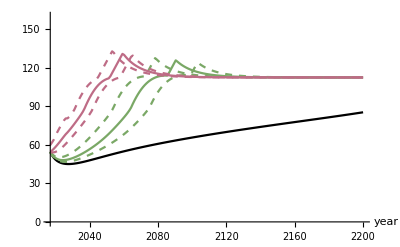

development

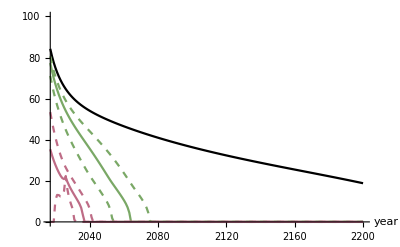

developed fossil stock

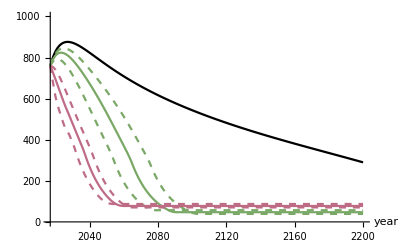

energy use

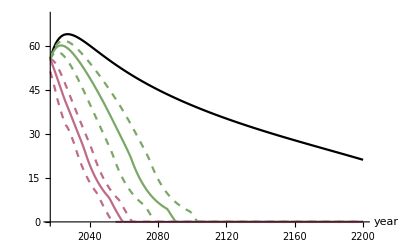

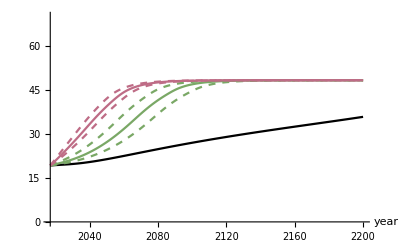

CCS

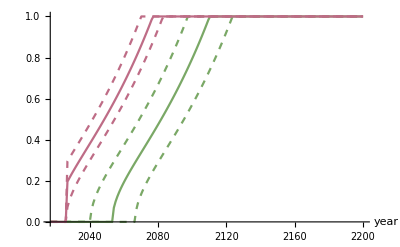

cumulative emissions

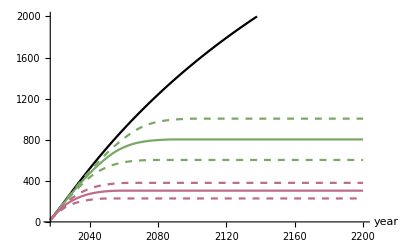

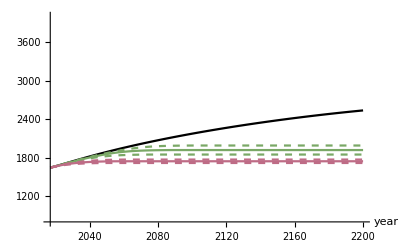

cumulative development

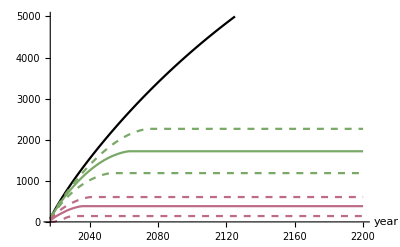

```mathematica
Figure output;

Print["prices"];
figP=ListLinePlot[{allp[[1]][[1;;maxt]],allp[[2]][[1;;maxt]], allp[[3]][[1;;maxt]], allp[[4]][[1;;maxt]], allp[[5]][[1;;maxt]], allp[[6]][[1;;maxt]], allp[[7]][[1;;maxt]]}, AxesLabel->{"year"," "}, DataRange->{2017,Y}, PlotRange->{0,160}, AxesOrigin->{2017,0}, PlotStyle->{Black, {ColorData["DarkBands",0.25], Dashed}, ColorData["DarkBands",0.25], {ColorData["DarkBands",0.25], Dashed}, {ColorData["DarkBands",0.4], Dashed}, ColorData["DarkBands",0.4], {ColorData["DarkBands",0.4], Dashed}}]
Export["figP.jpg",figP, ImageResolution->exportDPI];

Print["development"];
figX=ListLinePlot[{allX[[1]][[1;;maxt]],allX[[2]][[1;;maxt]], allX[[3]][[1;;maxt]], allX[[4]][[1;;maxt]], allX[[5]][[1;;maxt]], allX[[6]][[1;;maxt]], allX[[7]][[1;;maxt]]}, AxesLabel->{"year"," "}, DataRange->{2017,Y}, PlotRange->{0,100}, AxesOrigin->{2017,0}, PlotStyle->{Black, {ColorData["DarkBands",0.25], Dashed}, ColorData["DarkBands",0.25], {ColorData["DarkBands",0.25], Dashed}, {ColorData["DarkBands",0.4], Dashed}, ColorData["DarkBands",0.4], {ColorData["DarkBands",0.4], Dashed}}]
Export["figX.jpg",figX, ImageResolution->exportDPI];

Print["developed fossil stock"];
figS=ListLinePlot[{allS[[1]][[1;;maxt]],allS[[2]][[1;;maxt]], allS[[3]][[1;;maxt]], allS[[4]][[1;;maxt]], allS[[5]][[1;;maxt]], allS[[6]][[1;;maxt]], allS[[7]][[1;;maxt]]}, AxesLabel->{"year"," "}, DataRange->{2017,Y}, PlotRange->{0,1000}, AxesOrigin->{2017,0}, PlotStyle->{Black, {ColorData["DarkBands",0.25], Dashed}, ColorData["DarkBands",0.25], {ColorData["DarkBands",0.25], Dashed}, {ColorData["DarkBands",0.4], Dashed}, ColorData["DarkBands",0.4], {ColorData["DarkBands",0.4], Dashed}}]
Export["figS.jpg",figS, ImageResolution->exportDPI];

Print["energy use"];
figEF=ListLinePlot[{allEF[[1]][[1;;maxt]], allEF[[2]][[1;;maxt]], allEF[[3]][[1;;maxt]], allEF[[4]][[1;;maxt]], allEF[[5]][[1;;maxt]], allEF[[6]][[1;;maxt]], allEF[[7]][[1;;maxt]]}, AxesLabel->{"year"," "}, DataRange->{2017,Y}, PlotRange->{0,70}, AxesOrigin->{2017,0}, PlotStyle->{Black, {ColorData["DarkBands",0.25], Dashed}, ColorData["DarkBands",0.25], {ColorData["DarkBands",0.25], Dashed}, {ColorData["DarkBands",0.4], Dashed}, ColorData["DarkBands",0.4], {ColorData["DarkBands",0.4], Dashed}}]
Export["figEF.jpg",figEF, ImageResolution->exportDPI];

figK=ListLinePlot[{allK[[1]][[1;;maxt]], allK[[2]][[1;;maxt]], allK[[3]][[1;;maxt]], allK[[4]][[1;;maxt]], allK[[5]][[1;;maxt]], allK[[6]][[1;;maxt]], allK[[7]][[1;;maxt]]}, AxesLabel->{"year"," "}, DataRange->{2017,Y}, PlotRange->{0,70}, AxesOrigin->{2017,0}, PlotStyle->{Black, {ColorData["DarkBands",0.25], Dashed}, ColorData["DarkBands",0.25], {ColorData["DarkBands",0.25], Dashed}, {ColorData["DarkBands",0.4], Dashed}, ColorData["DarkBands",0.4], {ColorData["DarkBands",0.4], Dashed}}]
Export["figK.jpg",figK, ImageResolution->exportDPI];

Print["cumulative emissions"];
allcumF=0.35*allcumF;
allcumFH=0.35*allcumF+475/0.29;

figcumF=ListLinePlot[{allcumF[[1]][[1;;maxt]],allcumF[[2]][[1;;maxt]], allcumF[[3]][[1;;maxt]],allcumF[[4]][[1;;maxt]], allcumF[[5]][[1;;maxt]],allcumF[[6]][[1;;maxt]], allcumF[[7]][[1;;maxt]]}, AxesLabel->{"year"," "}, DataRange->{2017,Y}, AxesOrigin->{2017,0}, PlotRange->{0,2000}, PlotStyle->{Black, {ColorData["DarkBands",0.25], Dashed}, ColorData["DarkBands",0.25], {ColorData["DarkBands",0.25], Dashed}, {ColorData["DarkBands",0.4], Dashed}, ColorData["DarkBands",0.4], {ColorData["DarkBands",0.4], Dashed}}]
Export["figcumF_emissions.jpg",figcumF, ImageResolution->exportDPI];

figcumFH=ListLinePlot[{allcumFH[[1]][[1;;maxt]],allcumFH[[2]][[1;;maxt]], allcumFH[[3]][[1;;maxt]], allcumFH[[4]][[1;;maxt]],allcumFH[[5]][[1;;maxt]], allcumFH[[6]][[1;;maxt]], allcumFH[[7]][[1;;maxt]]}, AxesLabel->{"year"," "}, DataRange->{2017,Y}, AxesOrigin->{2017,800}, PlotRange->{800,4000},PlotStyle->{Black, {ColorData["DarkBands",0.25], Dashed}, ColorData["DarkBands",0.25], {ColorData["DarkBands",0.25], Dashed}, {ColorData["DarkBands",0.4], Dashed}, ColorData["DarkBands",0.4], {ColorData["DarkBands",0.4], Dashed}}]
Export["figcumFH_emissions.jpg",figcumFH, ImageResolution->exportDPI];

Print["cumulative development"];
figcumX=ListLinePlot[{allcumX[[1]][[1;;maxt]],allcumX[[2]][[1;;maxt]], allcumX[[3]][[1;;maxt]], allcumX[[4]][[1;;maxt]], allcumX[[5]][[1;;maxt]], allcumX[[6]][[1;;maxt]],  allcumX[[7]][[1;;maxt]]}, AxesLabel->{"year"," "}, DataRange->{2017,Y}, AxesOrigin->{2017,0}, PlotRange->{0,5000}, PlotStyle->{Black, {ColorData["DarkBands",0.25], Dashed}, ColorData["DarkBands",0.25], {ColorData["DarkBands",0.25], Dashed}, {ColorData["DarkBands",0.4], Dashed}, ColorData["DarkBands",0.4], {ColorData["DarkBands",0.4], Dashed}}]
Export["figcumX.jpg",figcumX, ImageResolution->exportDPI];


legend=LineLegend[{ColorData["DarkBands",0.25], ColorData["DarkBands",0.4], Black},{"2 degree budget", "1.5 degree budget", "laissez-faire"}];
Export["legend.jpg",legend, ImageResolution->exportDPI];
```

500

CCS

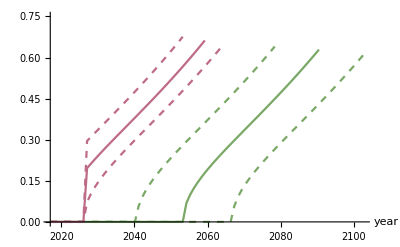

```mathematica
CCS share figure;
(* The model calculates the CCS share independent of fossil energy use. Yet, it is meaningful only if fossil energy use is strictly positive. The code below ensures the figure is consistent with this. *)

Z2h=Mean[FirstPosition[allEF[[2]],0]];
Z2m=Mean[FirstPosition[allEF[[3]],0]];
Z2l=Mean[FirstPosition[allEF[[4]],0]];
Z15h=Mean[FirstPosition[allEF[[5]],0]];
Z15m=Mean[FirstPosition[allEF[[6]],0]];
Z15l=Mean[FirstPosition[allEF[[7]],0]];
L=Length[allCCS[[1]]]

allCCS2h=allCCS[[1]];
allCCS2m=allCCS[[2]];
allCCS2l=allCCS[[3]];
allCCS15h=allCCS[[4]];
allCCS15m=allCCS[[5]];
allCCS15l=allCCS[[6]];

allCCS2h=Drop[allCCS2h,{Z2h,L}];
allCCS2m=Drop[allCCS2m,{Z2m,L}];
allCCS2l=Drop[allCCS2l,{Z2l,L}];
allCCS15h=Drop[allCCS15h,{Z15h,L}];
allCCS15m=Drop[allCCS15m,{Z15m,L}];
allCCS15l=Drop[allCCS15l,{Z15l,L}];

allCCS2h=PadRight[allCCS2h,L,Missing[]];
allCCS2m=PadRight[allCCS2m,L,Missing[]];
allCCS2l=PadRight[allCCS2l,L,Missing[]];
allCCS15h=PadRight[allCCS15h,L,Missing[]];
allCCS15m=PadRight[allCCS15m,L,Missing[]];
allCCS15l=PadRight[allCCS15l,L,Missing[]];
allCCS={allCCS2h,allCCS2m,allCCS2l,allCCS15h,allCCS15m,allCCS15l};
Export["ccs_budget.csv",allCCS];

Print["CCS"];
figCCS=ListLinePlot[{allCCS[[1]][[1;;maxt]], allCCS[[2]][[1;;maxt]], allCCS[[3]][[1;;maxt]], allCCS[[4]][[1;;maxt]], allCCS[[5]][[1;;maxt]], allCCS[[6]][[1;;maxt]]}, AxesLabel->{"year"," "}, DataRange->{2017,Y}, PlotRange->{0,0.75}, AxesOrigin->{2017,0}, PlotStyle->{{ColorData["DarkBands",0.25], Dashed}, ColorData["DarkBands",0.25], {ColorData["DarkBands",0.25], Dashed}, {ColorData["DarkBands",0.4], Dashed}, ColorData["DarkBands",0.4], {ColorData["DarkBands",0.4], Dashed}}]
Export["figccs.jpg",figCCS, ImageResolution->exportDPI];
```